```mathematica
SetDirectory["~/Desktop/ipcp/exercises/13/centralLimit"]
```

/home/zop/Desktop/ipcp/exercises/13/centralLimit

```mathematica
files = FileNames["*.txt"]
```

{10.txt,20.txt,2.txt,3.txt,50.txt,5.txt}

```mathematica
files = {"2.txt","3.txt","5.txt","10.txt","20.txt","50.txt"}
```

{2.txt,3.txt,5.txt,10.txt,20.txt,50.txt}

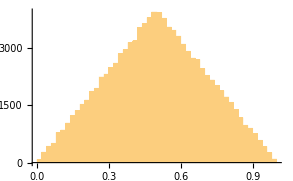
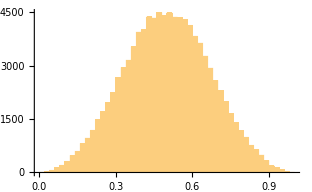
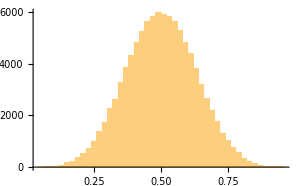
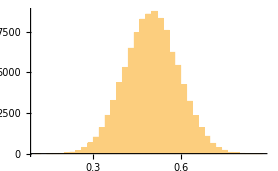
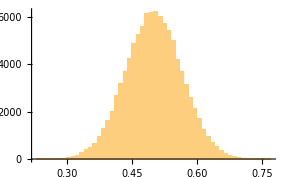
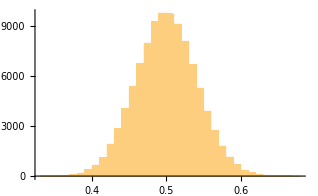

```mathematica
Histogram[ReadList[#],40]&/@files
```